```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

```mathematica
RawDataBCP=Import@GetZFileBCP[-1,1,1];
RawData0=Import@GetZFile[1,1,1];
RawData2=Import@GetZFile[-1,1,1];
ZBCP=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[{#1,#2 (1+√(1-#1^2)),#3}&@@@MapAt[N@Round[#,10^-3]&,RawDataBCP,{All,1}],First->(Drop[#,1]&)];
Z0=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData0,First->(Drop[#,1]&)];
Z2=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData2,First->(Drop[#,1]&)];
```

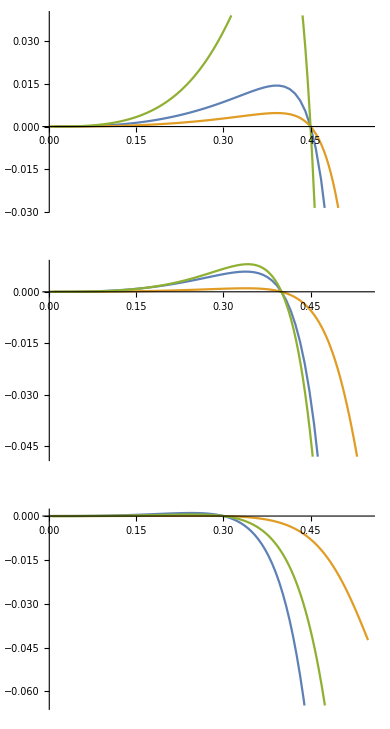

```mathematica
ListPlot[{ZBCP[#],Z0[#],Z2[#]},Joined->True,ImageSize->Medium]&/@{0.9,0.8,0.6}//GraphicsColumn
```